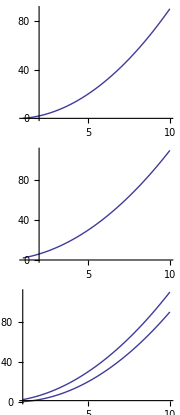

```mathematica
g1=Plot[x^2-x,{x,1,10},AspectRatio->0.6,AxesOrigin->Automatic];
g2=Plot[x^2+x,{x,1,10},AspectRatio->0.6,AxesOrigin->Automatic];
GraphicsColumn[{g1,g2,Show[g1,g2,AspectRatio->1,AxesOrigin->{1,1},PlotRange->All]},ImageSize->Small]
```

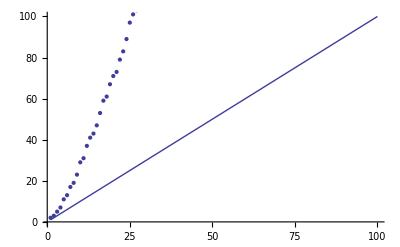

```mathematica
g1=Plot[x,{x,1,100}];
g2=ListPlot[Table[Prime[x],{x,1,100}]];
Show[g1,g2]
```

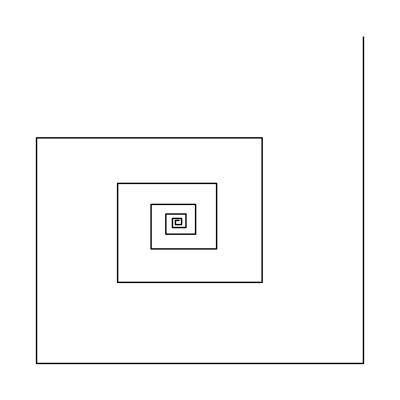

```mathematica
Graphics[Line[Partition[Flatten[{#,#} &/@ NestList[Cos,1.0,12]],2,1]]]
```

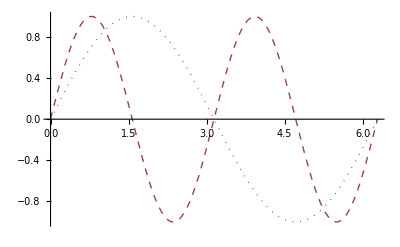

```mathematica
Needs["PlotLegends`"];
Plot[{Sin[x],Sin[2x]},{x,0,2π},PlotStyle->{Directive[Dotted],Directive[Dashed]},PlotLegend->{"Sin x","Sin 2x"},LegendPosition->{1,0.1},LegendSize->0.75]
```

```mathematica
NestList[Cos,1.0,12]
```

{1.,0.540302,0.857553,0.65429,0.79348,0.701369,0.76396,0.722102,0.750418,0.731404,0.744237,0.735605,0.741425}

```mathematica
Cos[Cos[1]]//N
```

0.857553

```mathematica
f[x_,y_]:=-1/(√(x^2+y^2))-5x;
g[x_,y_]:=-1/(√(x^2+y^2));
(*Plot3D[-1/(√(x^2+y^2))-1/x,{x, 0.001,1},{y, 0.001,1}]*)
(*e=1.6*10^-19
Plot3D[-e^2/(√(x^2+y^2)),{x, -1,1},{y, -1,1}]*)
Plot3D[f[x,y],{x, -1,1},{y, -1,1}, PlotRange->{-20,10}, Axes-> False, AspectRatio-> 1, Boxed->False,Mesh->15]
Plot3D[g[x,y],{x, -1,1},{y, -1,1}, PlotRange->{-20,10},Axes-> False, AspectRatio-> 1, Boxed->False,Mesh->5]
Plot3D[-1/(√(x^2+y^2))-x,{x, -1,1},{y, -1,1}];
(*RevolutionPlot3D[-1/(√(x^2+y^2))-1/x,{x, 0.001,1},{y, 0.001,1}]
RevolutionPlot3D[f[r],{r,0.001, 1}]*)
```

-Graphics3D-

-Graphics3D-

```mathematica
,PlotLabel->StyleForm["V(r)=-e^2/r-E(t)x",FontFamily->"Times",FontSize->12]
, PlotLabel->StyleForm["V(r)=-e^2/r",FontFamily->"Times",FontSize->12]
```

```mathematica
100!;
```

```mathematica
π 2^2;
N[π 2^2,4];
N[π 2^2];
N[π 2^2,100];
```

```mathematica
Expand[(x+y)^20];
Factor[%];
```

```mathematica
N[Sin[1000000],10];
```

```mathematica
Solve[{x+y==4,x-y==2},{x,y}];
```

```mathematica
DSolve[y'[x]==Cos[x],y[x],x];
```

```mathematica
LCM[2,3];
```

```mathematica
Reduce[{x+y+z==100,3x+2y+z/3==100,x>0,y>0,z>0},{x,y,z},Integers];
```

```mathematica
Rationalize[π,0.01];
```

```mathematica
Plot[{x/2,Sin[x]},{x,-π,π}];
```

```mathematica
fib[n_Integer] := Module[
{},
If[n<3,
Return[1],
Return[fib[n-1]+fib[n-2]]
];
]
fib[n_String]:=Module[
{},
Switch[n,
"一", Return[fib[1]],
"二", Return[fib[2]],
"三", Return[fib[3]],
_, Return["I don't knwo"]
]
]
fib[1];
fib[2];
fib[3];
fib[4];
fib["一"];
```

```mathematica
FindMax[lst:{Integer__}]:= Module[
	{index,i},
	index=1;

	For[i=2, i≤ Length[lst],i++,
	If[lst[i]>lst[[index]],
	index=i;
	Print["The max value has been updated to" <> ToString[i]<>"item"]]
	];

	Return[lst[[index]]]
];
FindMax[{1,2,3,6,9}];
```

```mathematica
Map[fib,Range[10]];
fib/@Range[10];
```

```mathematica
lst=Range[10];
For[i=1,i≤ Length[lst],i++,
lst[[i]]=fib[lst[[i]]]
];
lst;
```

```mathematica
Tan[#^2]&[1];
Tan[#^2]&/@{1,3,5,7,9};
```

```mathematica
{#1+#2,#1-#2}&[3,4];
```

```mathematica
Function[{x},Tan[x^2]]/@{1,3,5,7,9};
Function[{x,y},{x-y,x+y}]&[3,4]
```

Function[{x,y},{x-y,x+y}]

```mathematica
λ=Function;
λ[{x},Tan[x^2]]/@{1,3,5,7,9};
```

```mathematica
{#1+#2,#1-#2}&[Sequence @@ {1,2}];
```

```mathematica
SequenceMap[f_, lst_]:=f[Sequence @@ #]&/@lst;
SequenceMap[{#1+#2,#1-#2}&,{{1,2},{4,3}}];
```

```mathematica
MapIndexed[If[EvenQ[#2[[1]]],0,#1]&,Range[10]];
```

{1,0,3,0,5,0,7,0,9,0}

```mathematica
a+b//TreeForm;
```

```mathematica
142857 # &/@ Range[2,6];
N[1/Range[10],24];
```

(7.5×10^-6)/r^8-1.5/r

-1.5/r

(7.5×10^-6)/r^8

-0.00006/r^9+1.5/r^2

{{r→-0.212047+0.102117 ⅈ},{r→-0.212047-0.102117 ⅈ},{r→-0.0523713-0.229454 ⅈ},{r→-0.0523713+0.229454 ⅈ},{r→0.146741-0.184008 ⅈ},{r→0.146741+0.184008 ⅈ},{r→0.235355}}

-5.57669

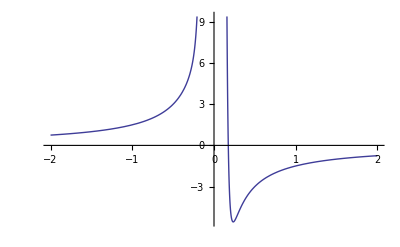

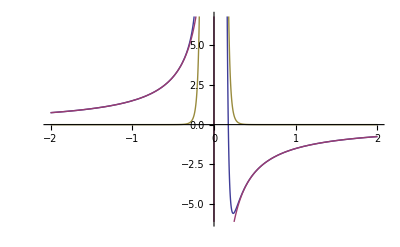

```mathematica
f[r_]=-1.5/r+(7.5*10^-6)/r^8
g[r_]=-1.5/r
h[r_]=(7.5*10^-6)/r^8
k[r_]=D[f[r],r]
Solve[k[r]==0]
f[0.235355]
Plot[{f[r]},{r,-2,2}]
Plot[{f[r],g[r],h[r]},{r,-2,2}]
```

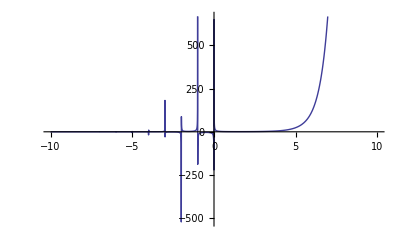

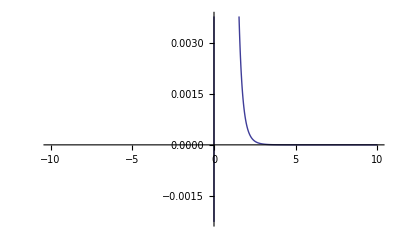

```mathematica
Plot[Gamma[x],{x,-10,10}]
Plot[Gamma[-5,x],{x,-10,10}]
```

```mathematica
?Gamma
```

Gamma[z] is the Euler gamma function Γ(z). 
Gamma[a,z] is the incomplete gamma function Γ(a,z). 
Gamma[a,z_0,z_1] is the generalized incomplete gamma function Γ(a,z_0)-Γ(a,z_1).

```mathematica
f[x_]=(1+a/x)^x
Limit[f[x],x->Infinity]
```

(1+a/x)^x

Plot::plln: Limiting value -∞ in {x, -∞, ∞} is not a machine-size real number.

Plot[f[1,x],{x,-∞,∞}]

ⅇ^a

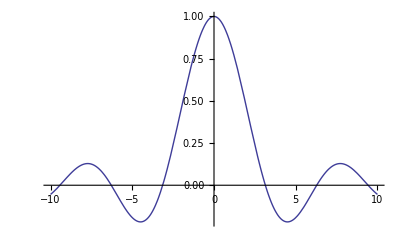

1

```mathematica
f[x_]:=Sin[x]/x
Plot[f[x],{x,-10,10}]
Limit[f[x],x->0]
```

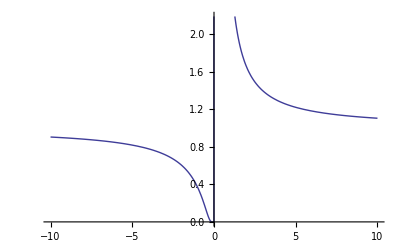

0

∞

```mathematica
f[x_]:=ⅇ^(1/x)
Plot[f[x],{x,-10,10}]
Limit[f[x],x->0,Direction->1]
Limit[f[x],x->0,Direction->-2]
```

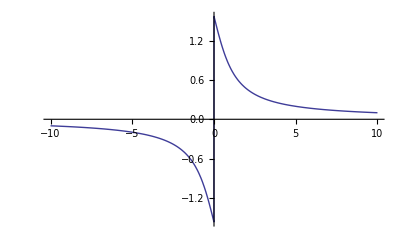

π/2

```mathematica
f[x_]:= ArcTan[1/x]
Plot[f[x],{x,-10,10}]
Limit[f[x],x->0,Direction->-1]
```

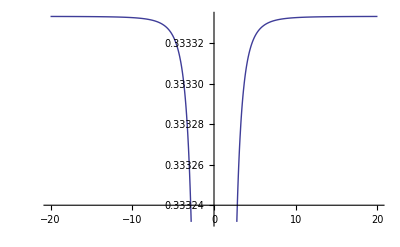

1/3

```mathematica
f[x_]:=x^2 Sin[1/(3 x^2)]
Plot[f[x],{x,-20,20}]
Limit[f[x],x->Infinity]
```

```mathematica
f[x_]:=ⅇ^(1/x)
Limit[f[x],x->0,Direction->-1]
```

∞

```mathematica
f[n_]:=(1-1/n)^n
Limit[f[n],n-> Infinity]
```

1/ⅇ

```mathematica
?N
```

N[expr] gives the numerical value of expr. 
N[expr,n] attempts to give a result with n-digit precision.

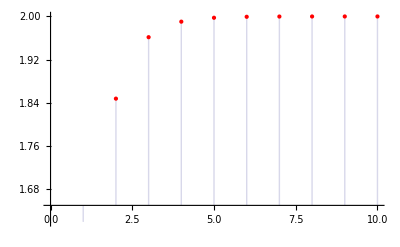

```mathematica
f[1]=Sqrt[2];
f[n_]:= √(2+f[n-1]);
x=Table[f[n],{n,1,10}];
ListPlot[x,PlotStyle->{Red,PointSize[Large]},Filling->Axis]
```

```mathematica
Clear[x];
f[x_]:=Sin[2 x^2+2];
D[f[x],x]
```

4 x Cos[2+2 x^2]

```mathematica
f[x]:=(2 x^2+3)Sin[x]
D[f[x],x]/.x->3
```

21 Cos[3]+12 Sin[3]

```mathematica
f[x_]:= Sin[2 x^2+3]
D[f[x],{x,2}]
D[f[x],{x,3}]
```

8 x Cos[x]+4 Sin[x]-(3+2 x^2) Sin[x]

12 Cos[x]-(3+2 x^2) Cos[x]-12 x Sin[x]

```mathematica
f[x_]=ⅇ^x Cos[2 x^2]
D[f[x],{x,2}]/.x->1
```

ⅇ^x Cos[2 x^2]

8 Cos[1]-Sin[1]

```mathematica
f[x]:=1/(x+1)
Do[Print[n,"  ",D[f[x],{x,n}]],{n,0,10}]
```

0  1/(1+x)

1  -1/(1+x)^2

2  2/(1+x)^3

3  -6/(1+x)^4

4  24/(1+x)^5

5  -120/(1+x)^6

6  720/(1+x)^7

7  -5040/(1+x)^8

8  40320/(1+x)^9

9  -362880/(1+x)^10

10  3628800/(1+x)^11

```mathematica
f[x_]:=1/(1+x)
Table[D[f[x],{x,n}],{n,0,10}]
Table[D[f[x],{x,n}],{n,0,10}]/.x->0
```

{1/(1+x),-1/(1+x)^2,2/(1+x)^3,-6/(1+x)^4,24/(1+x)^5,-120/(1+x)^6,720/(1+x)^7,-5040/(1+x)^8,40320/(1+x)^9,-362880/(1+x)^10,3628800/(1+x)^11}

{1,-1,2,-6,24,-120,720,-5040,40320,-362880,3628800}

```mathematica
Clear[x];
Do[Print[D[f[x],{x,n}]/.x->0],{n,0,10}]
```

1

-1

2

-6

24

-120

720

-5040

40320

-362880

3628800

```mathematica
Clear[x,y]
x[t_]:=2 t^2
y[t_]:=Sin[t]
f[t_]:=x'[t]/y'[t]
f[Pi/3]
```

(8 π)/3

```mathematica
F[x_,y_]:=1-x Exp[y]-y;
Fx=D[F[x,y],x]
Fy=D[F[x,y],y]
-Fx/Fy
Simplify[%]
```

-ⅇ^y

-1-ⅇ^y x

ⅇ^y/(-1-ⅇ^y x)

-ⅇ^y/(1+ⅇ^y x)

```mathematica
f[x_]:=4 x^3-5 x^2+x-2
a=(f[1]-f[0])/1-0
Solve[D[f[x],x]==a,x]
```

2+√2

{{x→(-2-√2-ⅈ √(2+√2))/(2+√2)},{x→(-2-√2+ⅈ √(2+√2))/(2+√2)}}

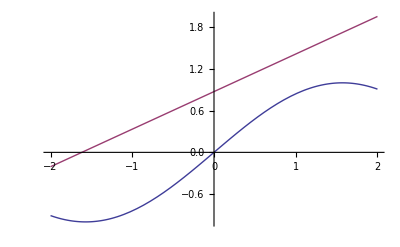

```mathematica
f[x_]:=Sin[x]
x0=1;
g[x_]:=f[x0]+f'[x0](x-x0)
Plot[{f[x],g[x]},{x,-2,2}]
```

3-2 x^2-y^2

-2

1-2 (-1+x)

1+1/2 (-1+x)

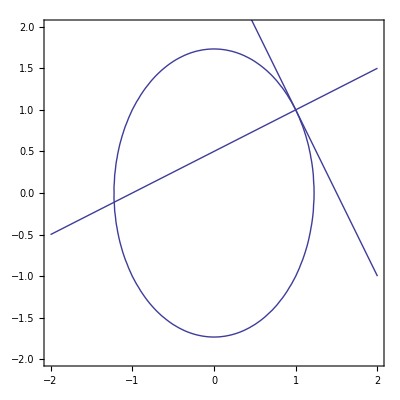

```mathematica
Clear[x,y];
F[x_,y_]=3-2 x^2-y^2
x0=1;
y0=1;
m=-D[F[x,y],x]/D[F[x,y],y]/.{x->x0,y->y0}
y=y0+m(x-x0)
y=y0-(1/m)(x-x0)
quxian=ContourPlot[F[x,y]==0,{x,-2,2},{y,-2,2}];
qiexian=Plot[y0+m(x-x0),{x,-2,2}];
faxian=Plot[y0-1/m(x-x0),{x,-2,2}];
Show[quxian,qiexian,faxian]
```

{{x→-0.885329-1.1418 ⅈ},{x→-0.885329+1.1418 ⅈ},{x→0.670657}}

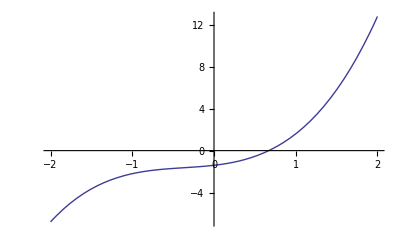

```mathematica
Clear[x,f]
f[x_]:=x^3+1.1 x^2+0.9x-1.4;
Solve[f[x]==0]
Plot[f[x],{x,-2,2}]
```

```mathematica
Clear[x,f]
f[x_]:=x^3+1.1 x^2+0.9x-1.4;
FindRoot[f[x]==0,{x,1}]
```

{x→0.670657}

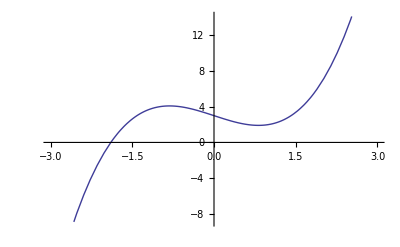

{{x→0}}

```mathematica
f[x_]:=x^3-2x+3
Plot[f[x],{x,-3,3}]
Solve[f''[x]==0,x]
```

x/(2+x^2)

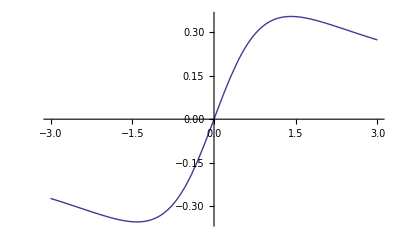

{{x→0},{x→-√6},{x→√6}}

```mathematica
Clear[f]
f[x_]=x/(2+x^2)
Plot[f[x],{x,-3,3}]
Solve[f''[x]==0,x]
```

```mathematica
f[x_]:=x^2+Sin[x]+1
Integrate[f[x],x]
```

x+x^3/3-Cos[x]

```mathematica
f[x_]:=x ArcTan[x]
Integrate[f[x],x]
```

-x/2+ArcTan[x]/2+1/2 x^2 ArcTan[x]

```mathematica
f[x_]:=x^2+Sin[x]+1
Integrate[f[x],{x,0,1}]
```

7/3-Cos[1]

```mathematica
f[x_]:=1/(√(1-x^2))
Integrate[f[x],x]
Integrate[f[x],{x,0,1/2}]
```

ArcSin[x]

π/6

```mathematica
f[x_]:=x ⅇ^(-2x)
Integrate[f[x],x]
Integrate[f[x],{x,0,Infinity}]
```

ⅇ^(-2 x) (-1/4-x/2)

1/4

```mathematica
f[x_]:=1/(1+x^2)
Integrate[f[x],x]
Integrate[f[x],{x,-Infinity,2}]
```

ArcTan[x]

π/2+ArcTan[2]

```mathematica
f[x_]:=1/(3+x^2)
Integrate[f[x],x]
Integrate[f[x],{x,-Infinity,Infinity}]
```

ArcTan[x/(√3)]/(√3)

π/(√3)

```mathematica
f[t_]:=tⅇ^-t
g[x_]:=Integrate[f[t],{t,0,x}]
D[g[x],x]
```

tⅇ^-x

```mathematica
f[t_]:=tⅇ^-t
g[x_]:=Integrate[f[t],{t,Log[x],x^2}]
D[g[x],x]//Simplify
```

-tⅇ^(-Log[x])/x+2 tⅇ^(-x^2) x

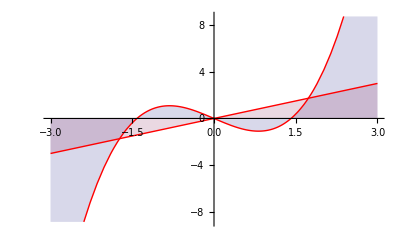

{{x→0},{x→-√3},{x→√3}}

9/4

```mathematica
Clear[f,g]
f[x_]:=x^3-2x
g[x_]:=x
Plot[{f[x],g[x]},{x,-3,3},PlotStyle->Red,Filling-> Axis]
Solve[f[x]-g[x]==0]
Integrate[g[x]-f[x],{x,0,√3}]
```

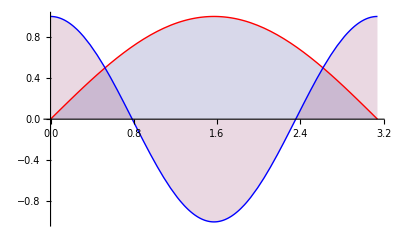

Solve::svars: Equations may not give solutions for all "solve" variables.

{{Cos[2 x]→Sin[x]}}

1/2 (-2+3 √3-2 Cos[1]-Sin[2])

0.603125

```mathematica
Clear[f,g]
f[x_]:=Sin[x]
g[x_]:=Cos[2x]
Plot[{f[x],g[x]},{x,0,π},PlotStyle->{Red,Blue},Filling-> Axis]
Solve[f[x]-g[x]==0]
A=Integrate[Abs[g[x]-f[x]],{x,0,1}]
N[A]
```

```mathematica
Clear[u,v,x,y,z,t]
f[v_]:=Sin[v];
x[u_,t_]:=f[u]Cos[t];
z[u_,t_]:=f[u]Sin[t];
y[u_,t_]:=u;
ParametricPlot3D[{x[u,t],y[u,t],z[u,t]},{u,0,2},{t,0,2},Mesh->50,PlotStyle->AbsoluteThickness[2],ViewPoint->{1,2,2},PlotStyle-> LightBlue]
```

-Graphics3D-

```mathematica
f[x_]:=Sin[x]
f[π/6]
f[x]/.x->π/6
```

1/2

1/2

```mathematica
f[x_,y_]=x^2 Sin[2*y];
D[f[x,y],x]
D[f[x,y],y]
```

2 x Sin[2 y]

2 x^2 Cos[2 y]

```mathematica
f[x_,y_]=x^2+3x y+y^2;
D[f[x,y],x]/.{x->1,y->2}
D[f[x,y],y]/.{x->1,y->2}
```

8

7

```mathematica
DSolve[y'[x]==2 x y[x],y[x],x]
```

{{y[x]→ⅇ^(x^2) C[1]}}

```mathematica
DSolve[{y'[x]==Exp[2 x -y[x]],y[0]==0},y[x],x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{y[x]→Log[1/2+ⅇ^(2 x)/2]}}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{y[x]→Log[1/2+ⅇ^(2 x)/2]}}

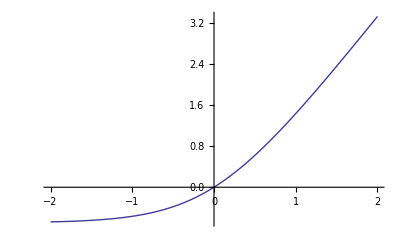

```mathematica
Jie=DSolve[{y'[x]==Exp[2 x -y[x]],y[0]==0},y[x],x]
Plot[y[x]/.Jie,{x,-2,2}]
```

```mathematica
Table[(1+n)/(1+n^2),{n,10}]
```

{1,3/5,2/5,5/17,3/13,7/37,4/25,9/65,5/41,11/101}

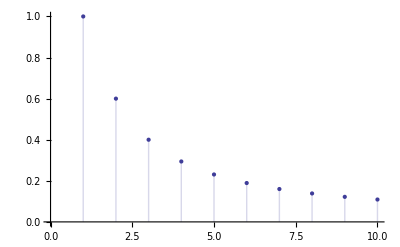

```mathematica
DiscretePlot[(1+n)/(1+n^2),{n,1,10}]
```

```mathematica
u[n_]:=1/n^4
Table[Sum[u[i],{i,1,n}],{n,1,10}]
Sum[u[n],{n,1,Infinity}]
```

{1,17/16,1393/1296,22369/20736,14001361/12960000,14011361/12960000,33654237761/31116960000,538589354801/497871360000,43631884298881/40327580160000,43635917056897/40327580160000}

π^4/90

```mathematica
Table[Plot3D[Sin[x y+t]Cos[y+t],{x,0,6},{y,0,6}],{t,0,2 Pi,0.4}];
Export["animation.gif",%]
```

animation.gif

```mathematica
DSolve[y'''[x]==Exp[2 x]-Cos[x],y[x],x]
```

{{y[x]→ⅇ^(2 x)/8+C[1]+x C[2]+x^2 C[3]+Sin[x]}}

```mathematica
Integrate[1/x,{x,-1,2},PrincipalValue->True]
```

Log[2]

```mathematica
Series[Exp[x],{x,0,5}]
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120+O[x]^6

```mathematica
Series[ⅇ^x/x^2,{x,0,4}]
```

1/x^2+1/x+1/2+x/6+x^2/24+x^3/120+x^4/720+O[x]^5

```mathematica
Series[Sin[x]/x^2,{x,0,4}]
```

1/x-x/6+x^3/120+O[x]^5

```mathematica
Series[ⅇ^(1/x),{x,-Infinity,3}]
```

1+1/x+1/(2 x^2)+1/(6 x^3)+O[1/x]^4

```mathematica
Sum[x^n/(n!),{n,0,k}]
```

(ⅇ^x Gamma[1+k,x])/(k!)

```mathematica
Product[x+n,{n,0,4}]
```

x (1+x) (2+x) (3+x) (4+x)

```mathematica
Residue[1/z,{z,0}]
```

1

```mathematica
Residue[Sin[z]/z,{z,0}]
```

0

```mathematica
Apart[1/((1+x)(2+x)(3+x))]
```

1/(2 (1+x))-1/(2+x)+1/(2 (3+x))

```mathematica
ZTransform[2^-n,n,z]
```

(2 z)/(-1+2 z)

```mathematica
DSolve[y''[x]+2y'[x]+y[x]==0,y[x],x]
```

{{y[x]→ⅇ^-x C[1]+ⅇ^-x x C[2]}}

```mathematica
DSolve[{y''[x]+2y'[x]+y[x]==0,y[0]==0},y[x],x]
```

{{y[x]→ⅇ^-x x C[2]}}

```mathematica
DSolve[y'[x]-2x y[x]==1,y[x],x]
```

{{y[x]→ⅇ^(x^2) C[1]+1/2 ⅇ^(x^2) √π Erf[x]}}

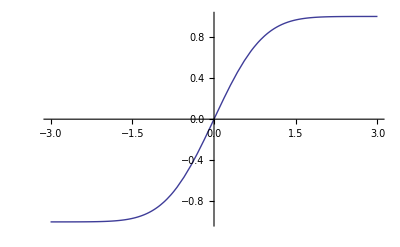

```mathematica
Plot[Erf[x],{x,-3,3}]
```

```mathematica
DSolve[x D[u[x,t],x]+t D[u[x,t],t]==Exp[x t],u[x, t],{x,t}]
```

{{u[x,t]→1/2 (ExpIntegralEi[t x]+2 C[1][t/x])}}

{1,4,9,16,25,36,49,64,81,100}

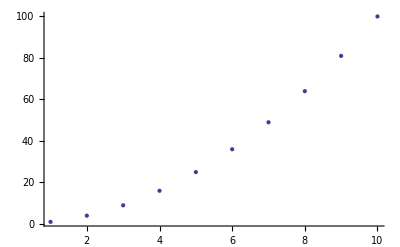

```mathematica
listofSquare=Table[j^2,{j,1,10}]
ListPlot[listofSquare]
```

```mathematica
{1,4,9,16,25,36,49,64,81,100}
```

```mathematica
Plot3D[1/3 x^3-x y^2,{x,-1,1},{y,-1,1}]
```

-Graphics3D-

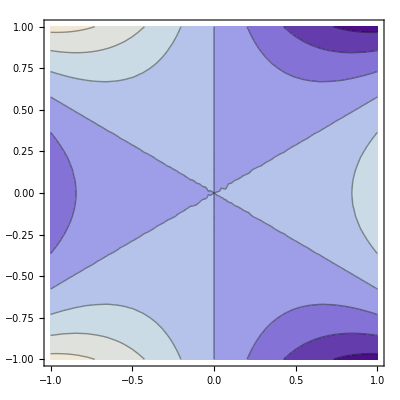

```mathematica
ContourPlot[1/3 x^3-x y^2,{x,-1,1},{y,-1,1}]
```

```mathematica
Plot[Sin[x]-1/x==0,x]
```

Plot::pllim: Range specification x is not of the form {x, xmin, xmax}.

Plot[Sin[x]-1/x==0,x]

```mathematica
FindRoot[Sin[x]-1/x,{x,6}]
```

{x→6.43912}

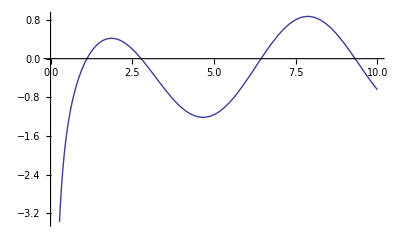

```mathematica
Plot[Sin[x]-1/x,{x,0,10}]
```

```mathematica
roots=Solve[x^2+3x+2==0,x]
f[x_]=4 x^2+3x
```

{{x→-2},{x→-1}}

```mathematica
f[x]/.roots[[1]]
```

-Sin[2]

```mathematica
v={1,2,3}
w={5,1,3}
```

{1,2,3}

{5,1,3}

```mathematica
v w
```

{5,2,9}

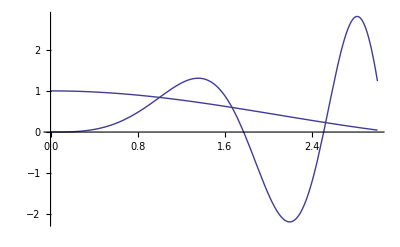

```mathematica
picture1=Plot[x Sin[x^2],{x,0,3}];
picture2=Plot[(1/x)Sin[x],{x,0,3}];
Show[picture1,picture2]
```

```mathematica
ParametricPlot3D[{Cos[t],Sin[t],t},{t,0,π}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{2Cos[θ]Sin[ϕ],3Sin[θ]Sin[ϕ],5Cos[ϕ]},{θ,0,2π},{ϕ,0,2π}]
```

-Graphics3D-

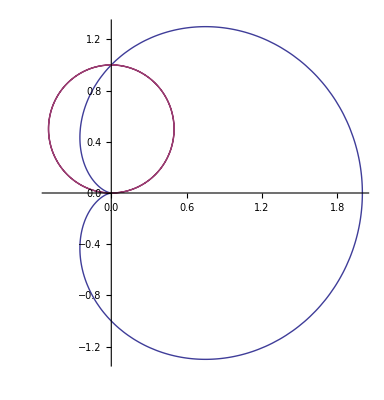

```mathematica
PolarPlot[{1+Cos[t],Sin[t]},{t,0,2Pi}]
```

```mathematica
f[x_]=Sin[x]+Cos[x]
f[3]//N
```

Cos[x]+Sin[x]

-0.848872

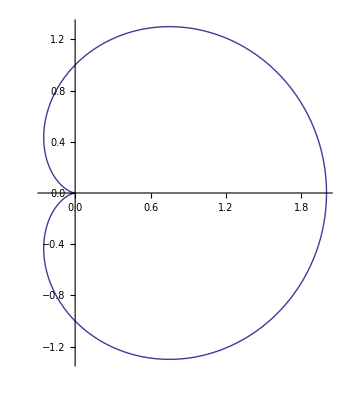

```mathematica
r1[t_]:=1+Cos[t]
PolarPlot[r1[t],{t,0,2π}]
```

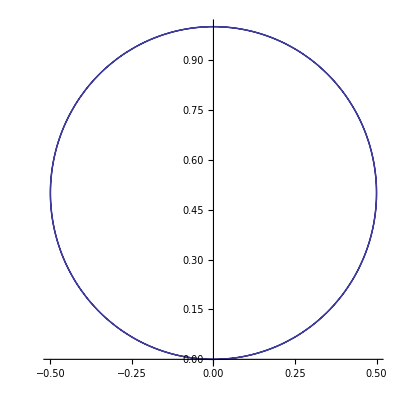
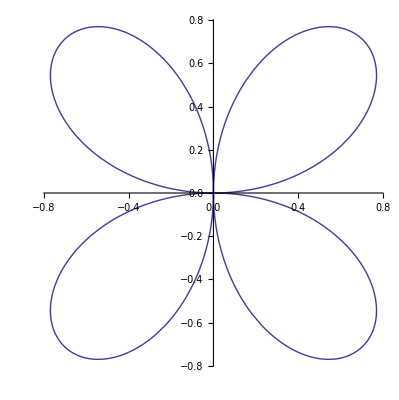
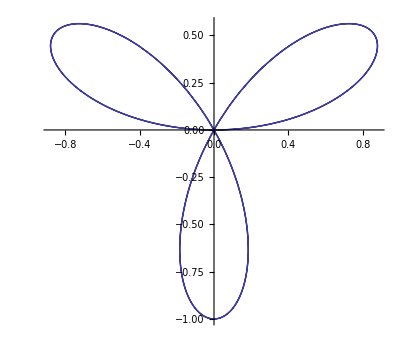
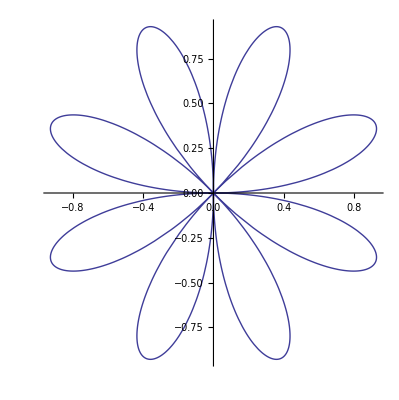
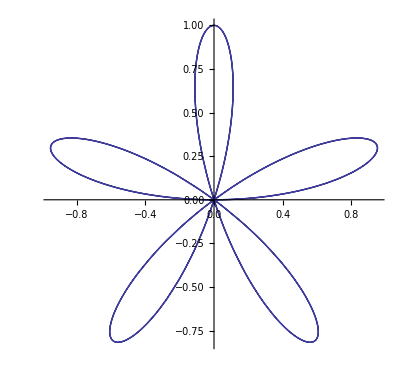

```mathematica
f[t_]:=Sin[a t]
Table[PolarPlot[f[t],{t,0,2π}],{a,1,5}]
```

```mathematica
Clear[f]
f[t_]:=Sin[a t]
Table[f[t],{a,0.8,0.2,2}]
```

{}

```mathematica
f[x_]:=x^2
Map[f,Range[1,10]]
f/@Range[1,11]
```

{1,4,9,16,25,36,49,64,81,100}

{1,4,9,16,25,36,49,64,81,100,121}

```mathematica
Tan[#^2]&[1]
```

Tan[1]

```mathematica
Map[Tan[#^2]&,Range[1,10]]
```

{Tan[1],Tan[4],Tan[9],Tan[16],Tan[25],Tan[36],Tan[49],Tan[64],Tan[81],Tan[100]}

```mathematica
f[x_]:= x^2
f[5]
5//f
```

25

25

```mathematica
f[x]/.x->5
```

25

```mathematica
f/. x->5
```

f

```mathematica
Clear[x,y]
DSolve[y'[x]==x+y[x],y[x],x]
```

DSolve::deqn: Equation or list of equations expected instead of True in the first argument True.

DSolve[True,y[x],x]

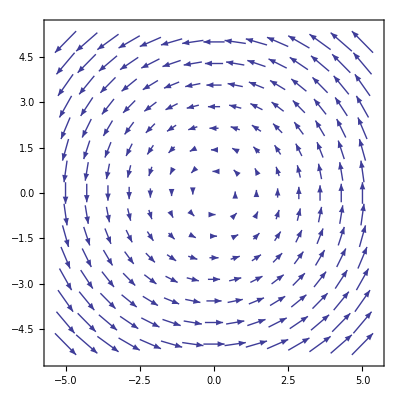

```mathematica
VectorPlot[{-y,x},{x,-5,5},{y,-5,5}]
```

```mathematica
Solution=DSolve[{y'[x]==x+y[x],y[0]==2},y[x],x]
```

DSolve::deqn: Equation or list of equations expected instead of True in the first argument {True, y[0] == 2}.

DSolve[{True,y[0]==2},y[x],x]

```mathematica
Series[√x,{x,2,5}]//Normal
```

√2+(-2+x)/(2 √2)-(-2+x)^2/(16 √2)+(-2+x)^3/(64 √2)-(5 (-2+x)^4)/(1024 √2)+(7 (-2+x)^5)/(4096 √2)

```mathematica
f[x_]=Exp[x];
Series[f[t],{t,0,n}]
p[n_,x_]:=Normal[Series[f[t],{t,0,n}]]/.t->x
Animate[Plot[{p[n,x],f[x]},{x,0,5}],{n,1,10,1}]
```

Series::serlim: Series order specification n is not a machine-size integer.

Series[ⅇ^t,{t,0,n}]

```mathematica
?Series
```

Series[f,{x,x_0,n}] generates a power series expansion for f about the point x=x_0 to order (x-x_0)^n. 
Series[f,{x,x_0,n_x},{y,y_0,n_y},…] successively finds series expansions with respect to x, then y, etc.

```mathematica
p1=Plot3D[Sin[x+y]Cos[x+y],{x,0,4},{y,0,4}]
```

-Graphics3D-

```mathematica
Show[p1,PlotRange->{-0.2,0.2}]
```

-Graphics3D-

```mathematica
Show[p1,FaceGrids->All]
```

-Graphics3D-

```mathematica
Show[p1,ViewPoint->{2,-2,0}]
```

-Graphics3D-

```mathematica
19^50
```

8663234049605954426644038200675212212900743262211018069459689001

```mathematica
19.^50
```

8.66323×10^63

```mathematica
Sin[Pi/4]^3 + Sin^3[Pi/4]
```

1/(2 √2)+Sin^(3[π/4])

```mathematica
N[ⅇ,60]
```

2.71828182845904523536028747135266249775724709369995957496697

```mathematica
125!
```

188267717688892609974376770249160085759540364871492425887598231508353156331613598866882932889495923133646405445930057740630161919341380597818883457558547055524326375565007131770880000000000000000000000000000000

```mathematica
Simplify[Cos[x]^4-Sin[x]^4]
```

Cos[2 x]

```mathematica
Needs["Graphics`Polyhedron`"]
```

Get::noopen: Cannot open Graphics`Polyhedron`.

Needs::nocont: Context Graphics`Polyhedron` was not created when Needs was evaluated.

$Failed

```mathematica
Show[Polyhedron[GreatStellatedDodecahedron]]
```

-Graphics3D-

-Graphics3D-

-Graphics-

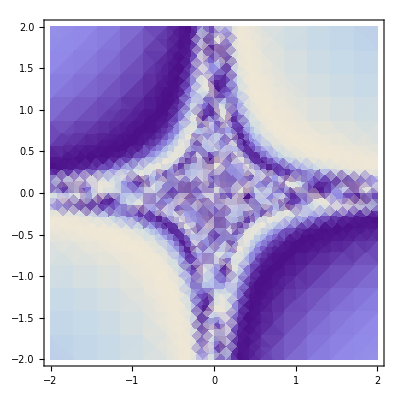

```mathematica
Plot3D[Sin[1/(x y)],{x,-2,2},{y,-2,2}]
ContourPlot[Sin[1/(x y)],{x,-2,2},{y,-2,2}]
DensityPlot[Sin[1/(x y)],{x,-2,2},{y,-2,2}]
```

```mathematica
a=Table[1/n,{n,1,10}]
```

{1,1/2,1/3,1/4,1/5,1/6,1/7,1/8,1/9,1/10}

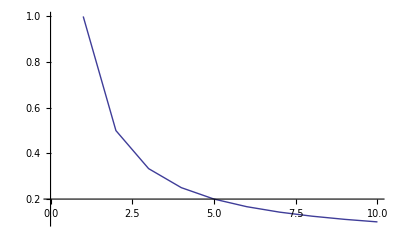

```mathematica
{1,1/2,1/3,1/4,1/5,1/6,1/7,1/8,1/9,1/10}
ListPlot[a,PlotJoined->True]
```

```mathematica
a={0, 1, 2, 0, -1};
ListPlot[a];
ListPlot[a,PlotStyle->PointSize[0.03]];
ListPlot[a,PlotStyle->{PointSize[0.03],Hue[0.9]}];
ListPlot[a,PlotStyle->{PointSize[0.03],Hue[0.9],PlotJoined->True}];
```

```mathematica
Clear[a];
a={{1,2,3},{4,5,6},{7,8,9}};
ListPlot3D[a,PlotStyle->PointSize[0.03]]
```

-Graphics3D-

```mathematica
a=Table[Sin[x y],{x,0,3π/2,π/15},{y,0,π/2,π/15}];
ListPlot3D[a]
ListPlot3D[a,Mesh->False]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

```mathematica
f[x_,y_]:= x^2+y^2
Dt[f[x,y]]
Dt[x^2+y^2]
```

2 x Dt[x]+2 y Dt[y]

2 x Dt[x]+2 y Dt[y]

{-10.22,11,-3.2,9.9}

-61.3221-43.0366 x+19.4111 x^2+88.806 Sin[x]

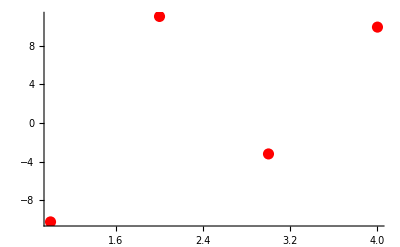

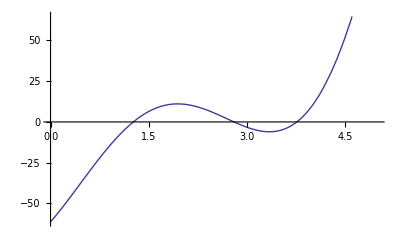

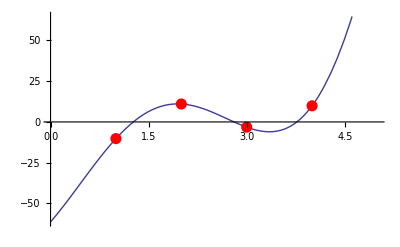

{-10.22,11.,-3.2,9.9}

```mathematica
a={-10.22,11,-3.2,9.9}
b=Fit[a,{1,x,x^2,Sin[x]},x]
ListPlot[a,PlotStyle->{PointSize[0.02],Hue[1]}]
Plot[b,{x,0,5}]
Show[%,%%]
{b/.x->1,b/.x->2, b/.x->3,b/.x->4}
```

```mathematica
b=Fit[{{1,2,1},{2,3,2},{3,4,3}},{x,y,x y},{x,y}]
Plot3D[b,{x,0,1},{y,0,1}];
```

1. x-6.59722×10^-16 y+0. x y

{{1.,1.},{4.,2.},{9.,3.},{16.,4.},{25.,5.},{36.,6.},{49.,7.},{64.,8.},{81.,9.},{100.,10.}}

InterpolatingFunction[{{1.,100.}},<>]

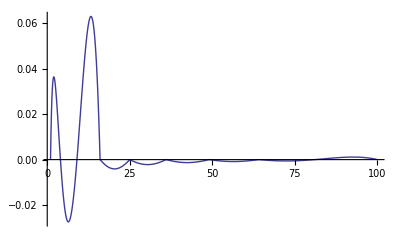

```mathematica
data1=Table[{y^2,y},{y,1.,10.}]
s=Interpolation[data1]
Plot[√x-s[x],{x,1,100},PlotRange->All]
```

```mathematica
FindMinimum[Sin[x]+x/5,{x,1}]
```

{-2.59086,{x→-8.05534}}

InterpolatingFunction[{{1,6}},<>]

2.4375

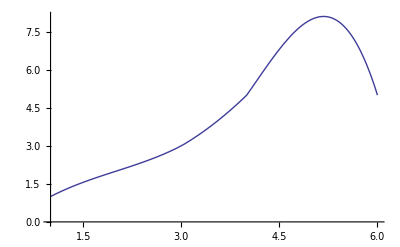

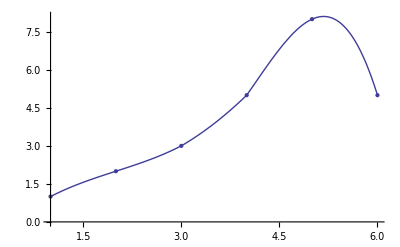

```mathematica
f=Interpolation[{1,2,3,5,8,5}]
f[2.5]
Plot[f[x],{x,1,6}]
Show[%,ListPlot[{1,2,3,5,8,5}]]
```

```mathematica
DSolve[D[u[x,y],x]+D[u[x,y],y]==0,u[x,y],{x,y}]
```

{{u[x,y]→C[1][-x+y]}}

```mathematica
DSolve[D[u[x,y],x]+D[u[x,y],y]-1/(x y)==0,u[x,y],{x,y}]
```

{{u[x,y]→(-Log[x]+Log[y]+x C[1][-x+y]-y C[1][-x+y])/(x-y)}}

```mathematica
DSolve[D[u[x,y],x]+D[u[x,y],y]==u[x,y]^2,u[x,y],{x,y}]
```

{{u[x,y]→1/(-x-C[1][-x+y])}}

```mathematica
DSolve[D[u[t,x],t,t]==a^2 D[u[t,x],x,x],u[t,x],{t,x}]
```

DSolve::nolist: List encountered within {SuperscriptBox[. There should be no lists on either side of the equations.

DSolve[u^(2,0)[t,x]=={104.448 u^(0,2)[t,x],121 u^(0,2)[t,x],10.24 u^(0,2)[t,x],98.01 u^(0,2)[t,x]},u[t,x],{t,x}]

```mathematica
DSolve[D[u[x,y],x,x]+D[u[x,y],y,y]==0,u[x,y],{x,y}]
```

{{u[x,y]→C[1][ⅈ x+y]+C[2][-ⅈ x+y]}}

```mathematica
f[x_]:=1/(√(2π))ⅇ^(-1/2 x^2)
∫_-1^1 f[x]ⅆx
N[%]
∫_-2^2 f[x]ⅆx
N[%]
∫_-3^3 f[x]ⅆx
N[%]
```

Erf[1/(√2)]

0.682689

Erf[√2]

0.9545

Erf[3/(√2)]

0.9973

```mathematica
∫_-3^3 f[x]ⅆx
```

Erf[3/(√2)]

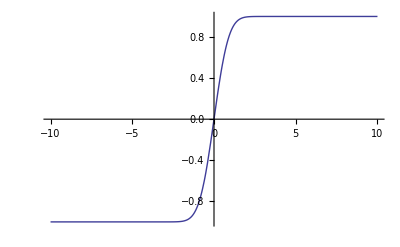

```mathematica
Plot[Erf[x],{x,-10,10}]
```